```mathematica
Trace[2-3*4]
```

{{{3 4,12},-12,-12},2-12,-10}

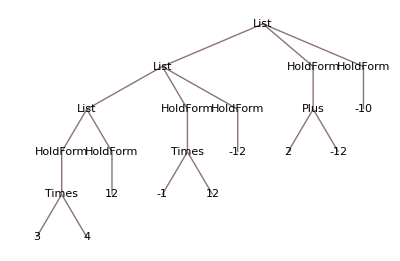

```mathematica
TreeForm[%32]
```

```mathematica
f=#1===#2&;
x=7;y=7;
Trace[f[x,y]]
```

{{f,#1===#2&},{x,7},{y,7},(#1===#2&)[7,7],7===7,True}

```mathematica
SetAttributes[g,HoldFirst];
g[a_,b_]:=a===b
Trace[g[x,y]]
```

{{y,7},g[x,7],x===7,{x,7},7===7,True}

```mathematica
SetAttributes[h,HoldFirst];
h[a_,b_]:=Unevaluated[a]===b
Trace[h[x,y]]
```

{{y,7},h[x,7],Unevaluated[x]===7,x===7,False}

```mathematica
Trace[Expand[(1+z)^2]==z^2+2z+1]
```

{{Expand[(1+z)^2],1+2 z+z^2},{z^2+2 z+1,1+2 z+z^2},1+2 z+z^2==1+2 z+z^2,True}